DensityPlot::cfun: The value of the option ColorFunction -> Inferno is not a valid color function or a gradient ColorData entity.

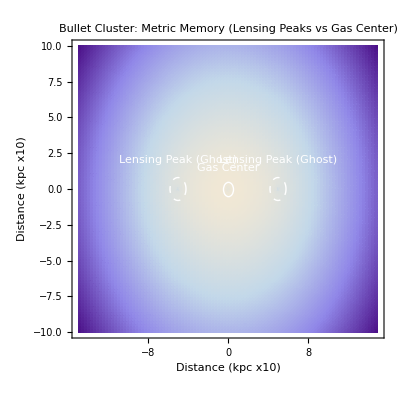

```mathematica
(*Grover Constants*)R=1.15428;
a0=1.2*10^-10; (*Grover Acceleration Scale*)
G=6.674*10^-11;

(*Normalized units for visualization:1 unit=10 kpc*)
Mgas=1.0; (*Stuck in the center*)
Mghost=0.8; (*The'Metric Memory' center*)
Lag=5.0; (*The physical offset observed in Bullet Cluster*)

(*The Grover Potential:Newton+Linear (Anomaly)*)
(*We use a soft-core potential to avoid singularities at r=0*)
Phi[x_,y_,Mx_,My_,mass_]:=Module[{r=Sqrt[(x-Mx)^2+(y-My)^2]+0.1},-(mass/r)-(mass*R*r)]

(*Define the two peaks:The Gas (Center) and the Ghosts (Lags)*)
TotalPotential[x_,y_]:=Phi[x,y,0,0,Mgas]+(*Central Gas*)Phi[x,y,-Lag,0,Mghost]+(*Left Ghost Peak*)Phi[x,y,Lag,0,Mghost];         (*Right Ghost Peak*)

(*Visualize the Gravitational Lensing Map*)
DensityPlot[TotalPotential[x,y],{x,-15,15},{y,-10,10},ColorFunction->"Inferno",PlotPoints->100,FrameLabel->{"Distance (kpc x10)","Distance (kpc x10)"},PlotLabel->"Bullet Cluster: Metric Memory (Lensing Peaks vs Gas Center)",Epilog->{White,Thick,Circle[{0,0},0.5],Text["Gas Center",{0,1.5}],Dashed,Circle[{-5,0},0.8],Circle[{5,0},0.8],Text["Lensing Peak (Ghost)",{-5,2}],Text["Lensing Peak (Ghost)",{5,2}]}]
```